```mathematica
Computations related to Table Section 13.2
By Le Chen.
Crated on Tue 19 Oct 2021 08:59:54 AM CDT
```

```mathematica
∫_(-∞)^d 1/(√(2π))Exp[-x^2/2]  ⅆ x
```

1/2 (1+Erf[d/(√2)])

```mathematica
First define functions
```

```mathematica
Clear["Global`*"]
n[d_]:=1/2 (1+Erf[d/(√2)])
d1 =(Log[S/K]+(r-δ+1/2 σ^2) (T-t))/(σ √(T-t));
d2 =d1 - σ √(T-t) ;
OptionCall[S_,t_]= S ⅇ^(-δ (T-t))n[d1] - K  ⅇ^(-r (T-t))n[d2];
OptionPut [S_,t_]= K  ⅇ^(-r (T-t))n[-d2] - S ⅇ^(-δ (T-t))n[-d1];
Δ[S_,t_]= D[OptionCall[S,t],S];
Γ[S_,t_]= D[OptionCall[S,t],{S,2}];
θ[S_,t_]= D[OptionCall[S,t],t];
```

```mathematica
Then define the constants (Setup)
```

```mathematica
K=40;
T=1;
t=T-91/365;
r=0.08;
σ=0.30;
δ=0;
```

```mathematica
Compute the Greeks and option price
```

```mathematica
OptionCall[40,t]
```

2.7804

```mathematica
Δ[40,t]
```

0.582404

```mathematica
Γ[40,t]
```

0.0651562

```mathematica
θ[40,t]
```

-6.33251

```mathematica
Case S increases to $40.75 and liquidate the position today
```

```mathematica
Option price insreased to
```

```mathematica
OptionCall[40.75,t]
```

3.23524

```mathematica
Profit should be
```

```mathematica
OptionCall[40,t]-OptionCall[40.75,t]
```

-0.454836

```mathematica
If we approximate using Δ, we would have
```

```mathematica
-(40.75-40) Δ[40,t]
```

-0.436803

```mathematica
New delta at S=40.75
```

```mathematica
Δ[40.75,t]
```

0.630078

```mathematica
Case S decreases to $39.25 and liquidate the position the same day
```

```mathematica
Option price declided to
```

```mathematica
OptionCall[39.25,t]
```

2.36218

```mathematica
Profit should be
```

```mathematica
OptionCall[40,t]-OptionCall[39.25,t]
```

0.418225

```mathematica
If we approximate using Δ, we would have
```

```mathematica
-(39.25-40) Δ[40,t]
```

0.436803

```mathematica
Hence, we need to use Γ to better approximate the changes.
```

```mathematica
Finally, plot the Option Call
```

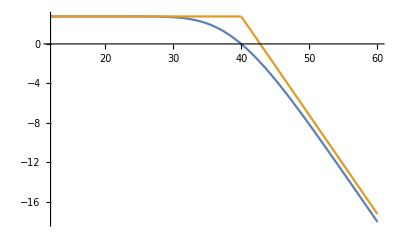

```mathematica
Plot[{OptionCall[40,t]-OptionCall[S,t],OptionCall[40,t]-Max[S-K,0]},{S,12,60}]
```